## Differences between primes

```mathematica
(*results={};*)
n=8;primes=allPrimes[[n]];
```

## Prime 8

```mathematica
diffs = Table[primes[[n+1]]-primes[[n]],{n,Length@primes-1}];
(* Removed first, 2 -> 3, the only transition with d = 1 *)
```

## Visibility Graph

```mathematica
visibles={};Do[
Do[
If[visibleQ[i,j,diffs],AppendTo[visibles,i->j],Null],
{j,i+1,Length@diffs}
],
{i,1,Length@diffs-1}];
```

## Graph

```mathematica
igv8=Graph[visibles, DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
adj=AdjacencyMatrix[igv8];
```

```mathematica
count = Total[adj]//Counts
```

<|1→1,3→1882,2→1373,7→595,6→921,4→1626,10→235,38→9,5→1264,11→215,9→345,8→475,13→153,19→46,16→73,12→176,33→6,29→19,18→54,58→1,25→18,20→34,64→2,104→1,14→113,17→58,28→11,15→75,24→17,21→35,32→9,31→11,46→4,27→11,55→4,35→6,40→6,26→19,39→2,23→29,22→28,44→4,41→2,34→4,51→1,70→1,57→3,62→1,71→1,30→6,42→2,37→2,54→1,50→1,43→3,56→1,47→1,45→1,36→1,53→1|>

```mathematica
count=count[[2;;]]
```

<|3→1882,2→1373,7→595,6→921,4→1626,10→235,38→9,5→1264,11→215,9→345,8→475,13→153,19→46,16→73,12→176,33→6,29→19,18→54,58→1,25→18,20→34,64→2,104→1,14→113,17→58,28→11,15→75,24→17,21→35,32→9,31→11,46→4,27→11,55→4,35→6,40→6,26→19,39→2,23→29,22→28,44→4,41→2,34→4,51→1,70→1,57→3,62→1,71→1,30→6,42→2,37→2,54→1,50→1,43→3,56→1,47→1,45→1,36→1,53→1|>

```mathematica
Sort[count]
```

<|58→1,104→1,51→1,70→1,62→1,71→1,54→1,50→1,56→1,47→1,45→1,36→1,53→1,64→2,39→2,41→2,42→2,37→2,57→3,43→3,46→4,55→4,44→4,34→4,33→6,35→6,40→6,30→6,38→9,32→9,28→11,31→11,27→11,24→17,25→18,29→19,26→19,22→28,23→29,20→34,21→35,19→46,18→54,17→58,16→73,15→75,14→113,13→153,12→176,11→215,10→235,9→345,8→475,7→595,6→921,5→1264,2→1373,4→1626,3→1882|>

```mathematica
countrel = Table[{x,Lookup[count,x]/Length@diffs}, {x,Keys[count]}]
```

{{3,1882/9999},{2,1373/9999},{7,595/9999},{6,307/3333},{4,542/3333},{10,235/9999},{38,1/1111},{5,1264/9999},{11,215/9999},{9,115/3333},{8,475/9999},{13,17/1111},{19,46/9999},{16,73/9999},{12,16/909},{33,2/3333},{29,19/9999},{18,6/1111},{58,1/9999},{25,2/1111},{20,34/9999},{64,2/9999},{104,1/9999},{14,113/9999},{17,58/9999},{28,1/909},{15,25/3333},{24,17/9999},{21,35/9999},{32,1/1111},{31,1/909},{46,4/9999},{27,1/909},{55,4/9999},{35,2/3333},{40,2/3333},{26,19/9999},{39,2/9999},{23,29/9999},{22,28/9999},{44,4/9999},{41,2/9999},{34,4/9999},{51,1/9999},{70,1/9999},{57,1/3333},{62,1/9999},{71,1/9999},{30,2/3333},{42,2/9999},{37,2/9999},{54,1/9999},{50,1/9999},{43,1/3333},{56,1/9999},{47,1/9999},{45,1/9999},{36,1/9999},{53,1/9999}}

```mathematica
countrel = countrel[[2;;]]
```

```mathematica
countrel={{2,1373/9999},{7,595/9999},{6,307/3333},{4,542/3333},{10,235/9999},{38,1/1111},{5,1264/9999},{11,215/9999},{9,115/3333},{8,475/9999},{13,17/1111},{19,46/9999},{16,73/9999},{12,16/909},{33,2/3333},{29,19/9999},{18,6/1111},{58,1/9999},{25,2/1111},{20,34/9999},{64,2/9999},{104,1/9999},{14,113/9999},{17,58/9999},{28,1/909},{15,25/3333},{24,17/9999},{21,35/9999},{32,1/1111},{31,1/909},{46,4/9999},{27,1/909},{55,4/9999},{35,2/3333},{40,2/3333},{26,19/9999},{39,2/9999},{23,29/9999},{22,28/9999},{44,4/9999},{41,2/9999},{34,4/9999},{51,1/9999},{70,1/9999},{57,1/3333},{62,1/9999},{71,1/9999},{30,2/3333},{42,2/9999},{37,2/9999},{54,1/9999},{50,1/9999},{43,1/3333},{56,1/9999},{47,1/9999},{45,1/9999},{36,1/9999},{53,1/9999}}
```

{{2,1373/9999},{7,595/9999},{6,307/3333},{4,542/3333},{10,235/9999},{38,1/1111},{5,1264/9999},{11,215/9999},{9,115/3333},{8,475/9999},{13,17/1111},{19,46/9999},{16,73/9999},{12,16/909},{33,2/3333},{29,19/9999},{18,6/1111},{58,1/9999},{25,2/1111},{20,34/9999},{64,2/9999},{104,1/9999},{14,113/9999},{17,58/9999},{28,1/909},{15,25/3333},{24,17/9999},{21,35/9999},{32,1/1111},{31,1/909},{46,4/9999},{27,1/909},{55,4/9999},{35,2/3333},{40,2/3333},{26,19/9999},{39,2/9999},{23,29/9999},{22,28/9999},{44,4/9999},{41,2/9999},{34,4/9999},{51,1/9999},{70,1/9999},{57,1/3333},{62,1/9999},{71,1/9999},{30,2/3333},{42,2/9999},{37,2/9999},{54,1/9999},{50,1/9999},{43,1/3333},{56,1/9999},{47,1/9999},{45,1/9999},{36,1/9999},{53,1/9999}}

## Model fit

```mathematica
nlm=NonlinearModelFit[countrel,b x^-a,{a,b},x]
```

FittedModel[0.38947/x^1.08371]

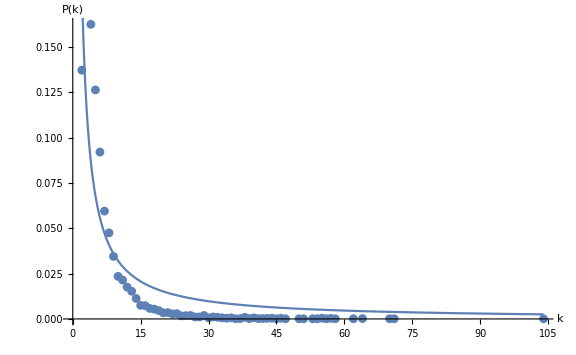

```mathematica
vis8=Show[
ListPlot[countrel,PlotRange->All,AxesOrigin->{0,0}],Plot[nlm[x],{x,0,Max[countrel[[All,1]]]},PlotRange->All,AxesOrigin->{0,0}],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large
]
```

```mathematica
Export[NotebookDirectory[]<>"v-8.eps",vis8];
```

## Mean degree

```mathematica
degree=VertexDegree[igv8]//Mean//N;
```

## Record result

```mathematica
(*AppendTo[results, Flatten[{"visibility", ToString@n,Length@diffs, degree,ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@nlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}]];*)
```

## Horizontal Visibility Graph

```mathematica
horizontals={};Do[
Do[
If[horizontalQ[i,j,diffs],AppendTo[horizontals,i->j],Null],
{j,i+1,Length@diffs}
],
{i,1,Length@diffs-1}];
```

## Graph

```mathematica
igh8=Graph[horizontals, VertexLabels->"Name",DirectedEdges->False,VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
adj=AdjacencyMatrix[igh8];
```

```mathematica
count = Total[adj]//Counts
```

<|1→2,3→2159,2→4064,5→866,6→576,12→33,7→338,4→1432,9→128,11→52,15→6,8→225,10→76,19→2,14→15,13→21,18→3,20→1|>

```mathematica
countrel = Table[{x,Lookup[count,x]/Length@diffs}, {x,Keys[count]}][[2;;]]
```

```mathematica
countrel={{3,2159/9999},{2,4064/9999},{5,866/9999},{6,64/1111},{12,1/303},{7,338/9999},{4,1432/9999},{9,128/9999},{11,52/9999},{15,2/3333},{8,25/1111},{10,76/9999},{19,2/9999},{14,5/3333},{13,7/3333},{18,1/3333},{20,1/9999}}
```

{{3,2159/9999},{2,4064/9999},{5,866/9999},{6,64/1111},{12,1/303},{7,338/9999},{4,1432/9999},{9,128/9999},{11,52/9999},{15,2/3333},{8,25/1111},{10,76/9999},{19,2/9999},{14,5/3333},{13,7/3333},{18,1/3333},{20,1/9999}}

## Model fit

```mathematica
nlm=NonlinearModelFit[countrel,b x^-a,{a,b},x];
```

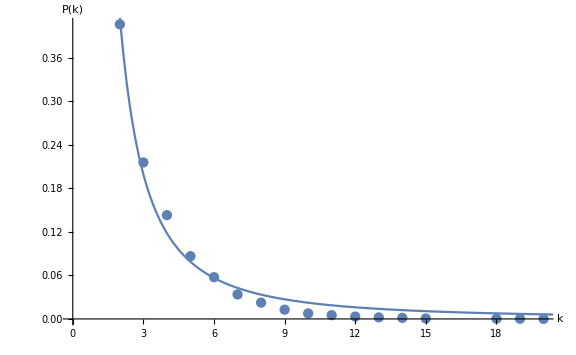

```mathematica
hvis8=Show[
ListPlot[countrel,PlotRange->All,AxesOrigin->{0,0}],Plot[nlm[x],{x,0,Max[Keys[count]]},PlotRange->All,AxesOrigin->{0,0}],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large
]
```

```mathematica
Export[NotebookDirectory[]<>"hv-8.eps",hvis8];
```

## Mean degree

```mathematica
degree=VertexDegree[igh8]//Mean//N;
```

## Record result

```mathematica
(*AppendTo[results, Flatten[{"horizontal", ToString@n,Length@diffs, degree,ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@nlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}]];*)
```

## Return result

```mathematica
results
```

{}